# Simple model of CRISPR dynamics

## General equations for concentrations

These are the “most general” equations for one spacer per cell and arbitrarily many spacer types, written in terms of concentrations as opposed to fractions of population.

```mathematica
getConcentrationEquations[nspacers_]:=Join[
{n[0]'[t]==f[0]n[0][t]-ρ p[0]v[t]n[0][t]-v[t]n[0][t]Sum[α[i],{i,1,nspacers}]+Sum[λ[i]n[i][t],{i,1,nspacers}]},
Table[
n[i]'[t]==f[i]n[i][t]-ρ p[i]v[t]n[i][t]+α[i]v[t]n[0][t]-λ[i]n[i][t],
{i,1,nspacers}],
{v'[t]==ρ v[t]Sum[(p[μ]m[μ]-1)n[μ][t],{μ,0,nspacers}]}
];
```

For these equations to be meaningfully used, we need a way of controlling growth. The simplest thing to do so is to make sure that the fitnesses go to zero as the total population reaches a certain value:

```mathematica
finiteGrowthRules[nspacers_]:=Table[f[μ]->f[μ](1-ntot/nmax),{μ,0,nspacers}]/.ntot->Sum[n[ν][t],{ν,0,nspacers}];
```

## General equations for fractions

Set up the “most general” equations for one spacer per cell, for an arbitrary number of spacer types.

```mathematica
getEquations[nspacers_]:=Join[
{x[0]'[t]==(f[0]-favg)x[0][t]-ρ(p[0]-pavg)v[t]x[0][t]-
			v[t]x[0][t]Sum[α[i],{i,1,nspacers}]+
			Sum[λ[i]x[i][t],{i,1,nspacers}]} (* wildtype *),
Table[x[i]'[t]==(f[i]-favg)x[i][t]-ρ(p[i]-pavg)v[t]x[i][t]+
			α[i]v[t] x[0][t]-λ[i]x[i][t],{i,1,nspacers}] (* spacer type i *),
{v'[t]==ρ v[t] ntot[t] Sum[(p[ν]m[ν]-1)x[ν][t],{ν,0,nspacers}]} (* phage *),
{ntot'[t]==ntot[t] (favg - ρ v[t] pavg)} (* total bacterial population *)
]/.(favg->Sum[f[μ]x[μ][t],{μ,0,nspacers}])/.pavg->(Sum[p[μ]x[μ][t],{μ,0,nspacers}]);
```

```mathematica
getConstraint[nspacers_]:=(Sum[x[i][t],{i,0,nspacers}]==1);
```

#### Tests

The equations as written above are somewhat difficult to check, so let’s see that some special cases work out nicely.

Test 1. Only wildtype.

```mathematica
testOnlyWTExpected={xwt'[t]==0, v'[t]==ρ v[t] ntot[t](pwt mwt-1),ntot'[t]==ntot[t](fwt-ρ v[t] pwt)};
```

```mathematica
testOnlyWTRule1=Solve[getConstraint[0], x[0][t]][[1]];
```

```mathematica
testOnlyWTRules=Solve[(getEquations[0]/.testOnlyWTRule1/.x[0]->xwt/.p[0]->pwt/.m[0]->mwt/.f[0]->fwt//Simplify),{xwt'[t],v'[t],ntot'[t]}][[1]];
```

```mathematica
And@@(testOnlyWTExpected/.testOnlyWTRules//Simplify)
```

True

Test 2. One spacer.

```mathematica
testOneSpacerExpected={x[0]'[t]==(f[0]-f[1])(1-x[0][t])x[0][t]-ρ(p[0]-p[1])(1-x[0][t])v[t]x[0][t]-v[t]x[0][t]α[1]+λ[1](1-x[0][t]),
x[1]'[t]==(f[1]-f[0])x[1][t](1-x[1][t])-ρ(p[1]-p[0])x[1][t]v[t](1-x[1][t])+α[1]v[t](1-x[1][t])-λ[1]x[1][t],
v'[t]==ρ v[t]ntot[t](p[0]m[0]x[0][t]+p[1]m[1](1-x[0][t])-1),
ntot'[t]==ntot[t](f[0]x[0][t]+f[1]x[1][t]-ρ v[t](p[0]x[0][t]+p[1]x[1][t]))
};
```

```mathematica
testOneSpacerRule1=Solve[getConstraint[1],x[1][t]][[1]];
```

```mathematica
testOneSpacerRules=Solve[getEquations[1]/.testOneSpacerRule1,{x[0]'[t],x[1]'[t],v'[t],ntot'[t]}][[1]]//Simplify
```

{x[0]'[t]→λ[1]+(f[0]-f[1]-v[t] (ρ p[0]-ρ p[1]+α[1])-λ[1]) x[0][t]+(-f[0]+f[1]+ρ (p[0]-p[1]) v[t]) (x[0][t])^2,x[1]'[t]→-λ[1]+(-f[0]+f[1]+v[t] (ρ p[0]-ρ p[1]+α[1])+λ[1]) x[0][t]+(f[0]-f[1]+ρ (-p[0]+p[1]) v[t]) (x[0][t])^2,v'[t]→-ρ ntot[t] v[t] (1-m[1] p[1]+(-m[0] p[0]+m[1] p[1]) x[0][t]),ntot'[t]→-ntot[t] (-f[1]+(-f[0]+f[1]) x[0][t]+ρ v[t] (p[1]+(p[0]-p[1]) x[0][t]))}

```mathematica
And@@(testOneSpacerExpected/.testOneSpacerRules/.testOneSpacerRule1//Simplify)
```

True

Test 3. Check that ∑_(μ=0)^n (ẋ)_μ==0.

```mathematica
Assuming[getConstraint[6],Sum[x[μ]'[t],{μ,0,6}]/.(getEquations[6]/.(A_==B_)->(A->B))//Simplify]
```

0

Test 4. Two spacer types, no fitness differences in absence of phage, same spacer loss probability for everyone, burst sizes for all spacer-having cells are all the same.

```mathematica
testReducedModelExpected={
x[0]'[t]==-ρ(p[0]-pavg)v[t]x[0][t]-v[t]x[0][t]αtot+λ(1-x[0][t]),
x[1]'[t]==-ρ(p[1]-pavg)v[t]x[1][t]+α[1]v[t]x[0][t]-λ x[1][t],
x[2]'[t]==-ρ(p[2]-pavg)v[t]x[2][t]+α[2]v[t]x[0][t]-λ x[2][t],
v'[t]==ρ v[t] ntot[t](m[0]p[0]x[0][t]+μ(p[1]x[1][t]+p[2]x[2][t])-1),
ntot'[t]==ntot[t](f[0]-ρ v[t] pavg)
}/.pavg->Sum[p[ν]x[ν][t],{ν,0,2}]/.αtot->Sum[α[i],{i,1,2}];
```

```mathematica
testReducedModelReductionRules={f[1]->f[0],f[2]->f[0],λ[1]->λ,λ[2]->λ,m[1]->μ,m[2]->μ};
```

```mathematica
testReducedModelRules=Solve[getEquations[2]/.testReducedModelReductionRules,{x[0]'[t],x[1]'[t],x[2]'[t],v'[t],ntot'[t]}][[1]]//Simplify
```

{x[0]'[t]→(-f[0]+ρ p[0] v[t]) (x[0][t])^2+λ (x[1][t]+x[2][t])-x[0][t] (f[0] (-1+x[1][t]+x[2][t])+v[t] (ρ p[0]+α[1]+α[2]-ρ p[1] x[1][t]-ρ p[2] x[2][t])),x[1]'[t]→-x[1][t] (λ-f[0]+f[0] x[0][t]+f[0] x[1][t]+f[0] x[2][t])+v[t] (x[0][t] (α[1]+ρ p[0] x[1][t])+ρ x[1][t] (-p[1]+p[1] x[1][t]+p[2] x[2][t])),x[2]'[t]→-x[2][t] (λ-f[0]+f[0] x[0][t]+f[0] x[1][t]+f[0] x[2][t])+v[t] (ρ (p[1] x[1][t]+p[2] (-1+x[2][t])) x[2][t]+x[0][t] (α[2]+ρ p[0] x[2][t])),v'[t]→ρ ntot[t] v[t] ((-1+m[0] p[0]) x[0][t]+(-1+μ p[1]) x[1][t]+(-1+μ p[2]) x[2][t]),ntot'[t]→ntot[t] ((f[0]-ρ p[0] v[t]) x[0][t]+(f[0]-ρ p[1] v[t]) x[1][t]+(f[0]-ρ p[2] v[t]) x[2][t])}

```mathematica
And@@(Assuming[getConstraint[2],testReducedModelExpected/.testReducedModelRules//Simplify])
```

True

Test 5. Does this fit with the concentration equations?

Note that the following test works regardless of whether the fitness values f[μ] are themselves functions of population numbers or food resources etc.

```mathematica
testConcentrationMatchEqns=getConcentrationEquations[5];
```

```mathematica
testConcentrationMatchNtotRule=ntot'[t]->Evaluate[Sum[n[μ]'[t],{μ,0,5}]/.(testConcentrationMatchEqns/.(A_==B_)->(A->B))/.n[μ_]->(ntot[#]x[μ][#]&)//Simplify];
```

```mathematica
testConcentrationFractionEqns0=Assuming[ntot[t]>0,(testConcentrationMatchEqns/.n[μ_]->(ntot[#]x[μ][#]&)//Simplify)/.testConcentrationMatchNtotRule//Simplify];
```

```mathematica
testConcentrationFractionRules=Solve[testConcentrationFractionEqns0,Evaluate[Join[Table[x[μ]'[t],{μ,0,5}],{v'[t]}]]][[1]]//Simplify;
```

```mathematica
And@@(getEquations[5]/.testConcentrationFractionRules/.testConcentrationMatchNtotRule//Simplify)
```

True

## Equations for reduced model

```mathematica
reducedRules={λ[_]->λ,m[0]->m,m[i_?Positive]->μ,f[_]->f0};
```

Stationary state

Let us check our formulas for the stationary state of the model.

The following function takes the rules identifying the parameters of a given reduced model, and returns rules for the stationary state solution. One of the rules should be for the number of spacers, n.

```mathematica
getStationaryState[rules_]:=Module[{rStarRule, A,αtot,x0star,xiRules,pbar,n0},
n0=(nspacers/.rules);
αtot=Sum[α[i],{i,1,n0}]/.rules;
A=(αtot/ρ+(m p[0]-1)/μ)/.rules;
rStarRule=Select[NSolve[Evaluate[rstar Sum[(α[i] ρ^-1)/((p[i]-μ^-1)+A rstar),{i,1,n0}]/.rules]==1, rstar],(rstar/.#)>0 &];
(*Print[rStarRule];*)
rStarRule=rStarRule[[1]];
x0star=(rstar/(1+rstar)/.rStarRule);
xiRules=Table[x[i]->Evaluate[x0star (α[i] ρ^-1)/((p[i]-μ^-1)+A rstar)/.rStarRule/.rules],{i,1,n0}];
pbar=Sum[p[i]x[i]/.rules/.xiRules,{i,1,n0}];
Join[
{x[0]->x0star},
xiRules,
{v->Evaluate[(m λ)/(1-μ pbar)(m p[0]+μ pbar - 1)/(m(αtot+ρ(p[0]-pbar))-ρ(1-μ pbar))/.rules]}]
];
```

Numerical examples

## One spacer type

Let’s define some parameters.

```mathematica
numericalExampleRules={nspacers->1,f0->1.0,m->50,μ->10,λ->1*^-3,p[0]->0.99,p[1]->0.02,α[1]->1*^-7,ρ->1*^-3};
```

Find the predicted stationary state.

```mathematica
numericalExamplePredictedStationary=getStationaryState[numericalExampleRules]
```

{x[0]→0.0162272,x[1]→0.983773,v→63.5243}

And solve the equations numerically to see whether our prediction is right.

```mathematica
numericalExampleICs={x[0][0]==0.95,x[1][0]==0.05,v[0]==0.01,ntot[0]==100};
```

```mathematica
tmax=6;
```

```mathematica
numericalSoln=NDSolve[Evaluate[Join[numericalExampleICs,getEquations[nspacers/.numericalExampleRules]/.reducedRules/.numericalExampleRules]],Evaluate[Join[Table[x[i],{i,0,(nspacers/.numericalExampleRules)}],{v,ntot}]],{t,0,tmax}];
```

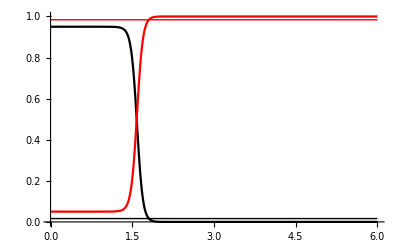

```mathematica
Plot[Evaluate[Join[{x[0][t],x[1][t]}/.numericalSoln,{x[0],x[1]}/.numericalExamplePredictedStationary]],{t,0,tmax},PlotRange->{0,1},PlotStyle->{Black,Red,{Thin, Black}, {Thin, Red}}]
```

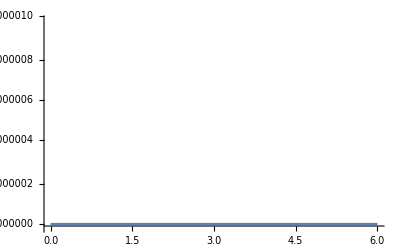

```mathematica
Plot[Evaluate[x[0][t]+x[1][t]]/.numericalSoln,{t,0,tmax}]
```

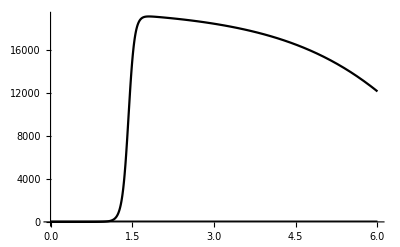

```mathematica
Plot[Evaluate[{v[t]/.numericalSoln,v/.numericalExamplePredictedStationary}],
{t,0,tmax}, PlotStyle->{Black,{Thin,Black}},PlotRange->All]
```

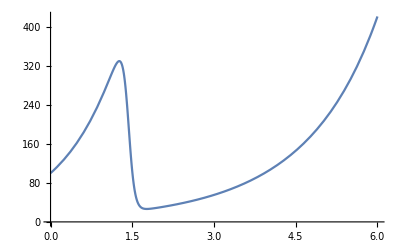

```mathematica
Plot[ntot[t]/.numericalSoln,{t,0,tmax}]
```

### Population with finite resources

Let’s see what happens when we cap the maximum size of our population.

```mathematica
capacityRule={nmax->1000};
```

```mathematica
numericalExampleConcEqns=getConcentrationEquations[nspacers/.numericalExampleRules]/.finiteGrowthRules[nspacers/.numericalExampleRules]/.reducedRules/.capacityRule;
```

```mathematica
numericalExampleConcICs={n[0][0]==95,n[1][0]==5,v[0]==0.01};
```

```mathematica
tmax=24;
```

```mathematica
numericalSoln=NDSolve[Evaluate[Join[numericalExampleConcICs,(numericalExampleConcEqns/.numericalExampleRules)]],Evaluate[Join[Table[n[i],{i,0,(nspacers/.numericalExampleRules)}],{v}]],{t,0,tmax}];
```

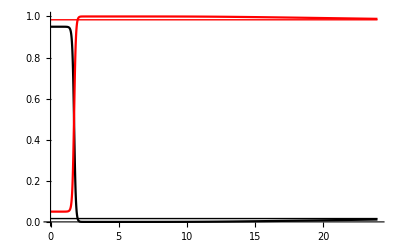

```mathematica
Plot[Evaluate[Join[{n[0][t],n[1][t]}/(n[0][t]+n[1][t])/.numericalSoln,{x[0],x[1]}/.numericalExamplePredictedStationary]],{t,0,tmax},PlotRange->{0,1},PlotStyle->{Black,Red,{Thin, Black}, {Thin, Red}}]
```

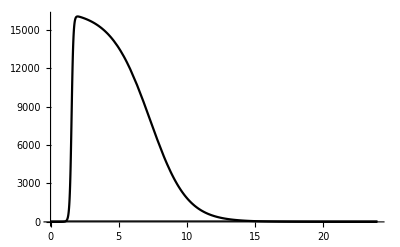

```mathematica
Plot[Evaluate[{v[t]/.numericalSoln,v/.numericalExamplePredictedStationary}],
{t,0,tmax}, PlotStyle->{Black,{Thin,Black}},PlotRange->All]
```

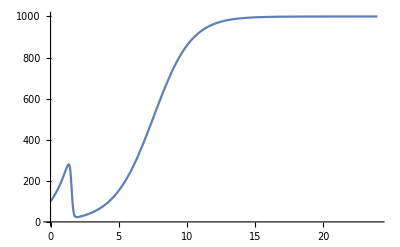

```mathematica
Plot[n[0][t]+n[1][t]/.numericalSoln,{t,0,tmax},PlotRange->{0,nmax/.capacityRule}]
```

## Two spacer types

Now let’s define some parameters.

```mathematica
(* Concentrations measured in 10^8 ml^-1;
	ρ measured in 10^-8 ml/hour;
	fitnesses and λ measured in hour^-1;
	α[i] measured in 10^-8 ml/hour; 
	time measured in hours; *)
```

```mathematica
numericalExampleRules={nspacers->2,f0->1.0,m->50,μ->10,λ->1*^-3,p[0]->0.99,p[1]->0.02,p[2]->0.01,α[1]->2*^-7,α[2]->1*^-7,ρ->1*^-3};
```

Find the predicted stationary state.

```mathematica
numericalExamplePredictedStationary=getStationaryState[numericalExampleRules]
```

{x[0]→0.0182179,x[1]→0.00036429,x[2]→0.981418,v→55.9941}

And solve the equations numerically to see whether our prediction is right.

```mathematica
numericalExampleICs={x[0][0]==1.0,x[1][0]==0,x[2][0]==0,v[0]==10,ntot[0]==1};
```

```mathematica
tmax=24;
```

```mathematica
numericalSoln=NDSolve[Evaluate[Join[numericalExampleICs,getEquations[nspacers/.numericalExampleRules]/.reducedRules/.numericalExampleRules]],Evaluate[Join[Table[x[i],{i,0,(nspacers/.numericalExampleRules)}],{v,ntot}]],{t,0,tmax}];
```

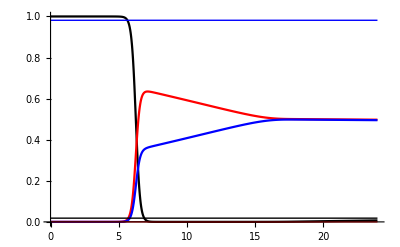

```mathematica
Plot[Evaluate[Join[{x[0][t],x[1][t],x[2][t]}/.numericalSoln,{x[0],x[1],x[2]}/.numericalExamplePredictedStationary]],{t,0,tmax},PlotRange->{0,1},PlotStyle->{Black,Red,Blue,{Thin, Black}, {Thin, Red}, {Thin,Blue}}]
```

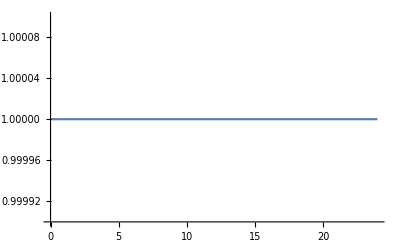

```mathematica
Plot[Evaluate[x[0][t]+x[1][t]+x[2][t]]/.numericalSoln,{t,0,tmax},PlotRange->{0.9999,1.0001}]
```

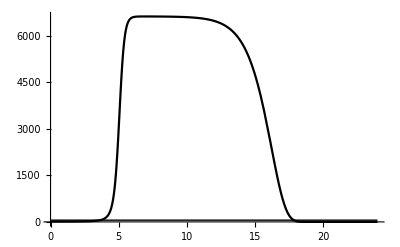

```mathematica
Plot[Evaluate[{v[t]/.numericalSoln,v/.numericalExamplePredictedStationary}],
{t,0,tmax}, PlotStyle->{Black,{Thin,Black}},PlotRange->All]
```

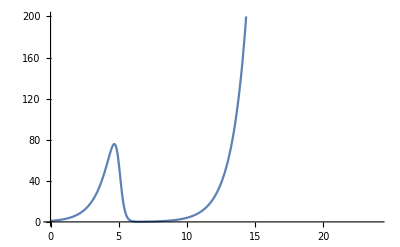

```mathematica
Plot[ntot[t]/.numericalSoln,{t,0,tmax}, PlotRange->{0,200}]
```

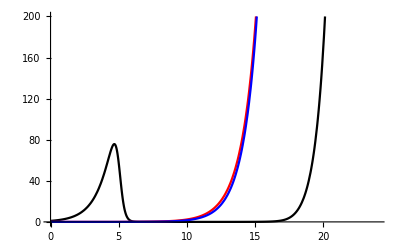

```mathematica
Plot[Evaluate[ntot[t]{x[0][t],x[1][t],x[2][t]}/.numericalSoln],{t,0,tmax},PlotStyle->{Black,Red,Blue}, PlotRange->{0,200}]
```

### Population with finite resources

Let’s see what happens when we cap the maximum size of our population.

```mathematica
capacityRule={nmax->400};
```

```mathematica
numericalExampleConcEqns=getConcentrationEquations[nspacers/.numericalExampleRules]/.finiteGrowthRules[nspacers/.numericalExampleRules]/.reducedRules/.capacityRule;
```

```mathematica
numericalExampleConcICs={n[0][0]==1.0,n[1][0]==0,n[2][0]==0,v[0]==10};
```

```mathematica
tmax=32;
```

```mathematica
numericalSoln=NDSolve[Evaluate[Join[numericalExampleConcICs,(numericalExampleConcEqns/.numericalExampleRules)]],Evaluate[Join[Table[n[i],{i,0,(nspacers/.numericalExampleRules)}],{v}]],{t,0,tmax}];
```

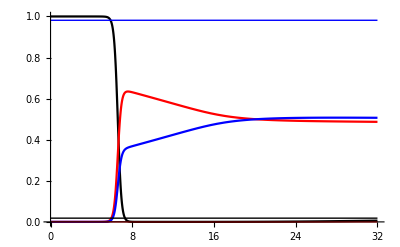

```mathematica
Plot[Evaluate[Join[{n[0][t],n[1][t],n[2][t]}/(n[0][t]+n[1][t]+n[2][t])/.numericalSoln,{x[0],x[1],x[2]}/.numericalExamplePredictedStationary]],{t,0,tmax},PlotRange->{0,1},PlotStyle->{Black,Red,Blue,{Thin, Black}, {Thin, Red}, {Thin,Blue}}]
```

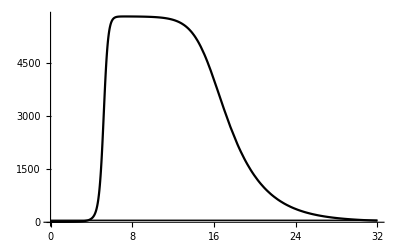

```mathematica
Plot[Evaluate[{v[t]/.numericalSoln,v/.numericalExamplePredictedStationary}],
{t,0,tmax}, PlotStyle->{Black,{Thin,Black}},PlotRange->All]
```

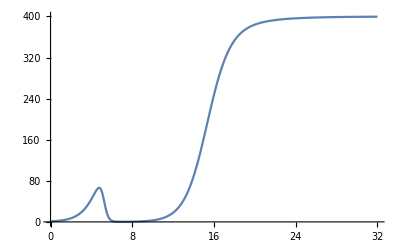

```mathematica
Plot[n[0][t]+n[1][t]+n[2][t]/.numericalSoln,{t,0,tmax},PlotRange->{0,nmax/.capacityRule}]
```

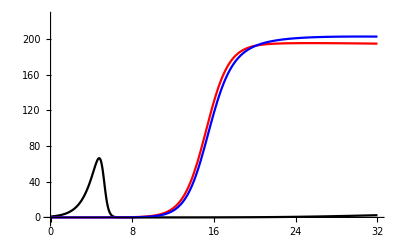

```mathematica
Plot[Evaluate[{n[0][t],n[1][t],n[2][t]}/.numericalSoln],{t,0,tmax},PlotStyle->{Black,Red,Blue}, PlotRange->{-5,225}]
```

## Noise

We have the covariance matrix of the Wiener process only in an implicit form, in terms of the diffusion tensor. We first define a function that calculates the diffusion tensor for a given number of spacers.

```mathematica
diffusionTensor[nspacers_]:=Join[{
Join[{(f[0]+ρ p[0]v[t]+αtot v[t])n[0][t]+Sum[λ[i]n[i][t],{i,1,nspacers}]},
Table[-α[i]v[t]n[0][t],{i,1,nspacers}],{-ρ p[0] m[0]v[t]n[0][t]}]},
Table[
Join[{-α[i]v[t]n[0][t]-λ[i]n[i][t]},Table[KroneckerDelta[i,j]((f[i]+ρ p[i]v[t])n[i][t] + α[i]v[t]n[0][t]+λ[i]n[i][t]),{j,1,nspacers}],{-ρ p[i] m[i] v[t] n[i][t]}],{i,1,nspacers}],
{Join[{-ρ p[0]m[0]v[t]n[0][t]},Table[-ρ p[i]m[i]v[t]n[i][t],{i,1,nspacers}],{Sum[ρ v[t] n[μ][t](p[μ] m[μ]^2+(1-p[μ])),{μ,0,nspacers}]}]
}]/.αtot->Sum[α[k],{k,1,nspacers}];
```

NOTE! The population numbers (n[μ], v) have to be expressed in actual numbers of individuals (instead of hundreds of millions or per-ml concentrations) in the calculation of the diffusion tensor. This is because the derivation assumed that the transitions occur by changing this number by 1.

```mathematica
MatrixPower[diffusionTensor[1]/.reducedRules/.n[μ_][t]->n[μ][t]/.v[t]->v[t]/.numericalExampleRules/.t->8/.numericalSoln[[1]],1/2]//MatrixForm
```

(0.0379199 | -0.00392937 | -0.0240459
-0.00443979 | 0.585849 | -0.101922
-0.0240629 | -0.101919 | 3.01986)

```mathematica
MatrixPower[diffusionTensor[1]/.reducedRules/.n[μ_][t]->10^8 n[μ][t]/.v[t]->10^8 v[t]/.numericalExampleRules/.t->8/.numericalSoln[[1]],1/2]/10^8//MatrixForm
```

(0.0243281 | -0.0162364 | -0.0246444
-0.0162364 | 0.151736 | -0.115984
-0.0246444 | -0.115984 | 3.01935)

```mathematica
{n[0][8],n[1][8],v[8]}/.numericalSoln[[1]]
```

{0.000254586,0.316568,5802.76}

It seems like for the kinds of numbers we’re using here, the effect from this kind of noise (which is simply due to the discrete nature of the problem) should be negligible. I don’t know exactly what the conditions are under which we can ignore the non-diagonal elements, but superficially they seem rather small.

Many spacers

Look at the distribution of frequencies for a bunch of spacers.

```mathematica
nSpacers=100;
```

```mathematica
deathRateDist=BetaDistribution[1.2, 15];
```

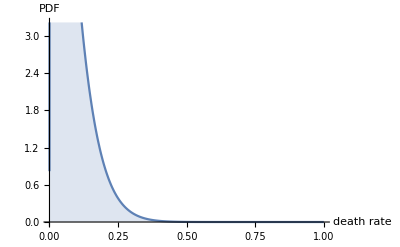

```mathematica
Plot[PDF[deathRateDist, x],{x,0,1},Filling->Axis, AxesLabel->{"death rate","PDF"}]
```

```mathematica
deathRates=RandomVariate[deathRateDist, nSpacers];
```

```mathematica
acquisitionDist=LogNormalDistribution[-15.5,1.0];
```

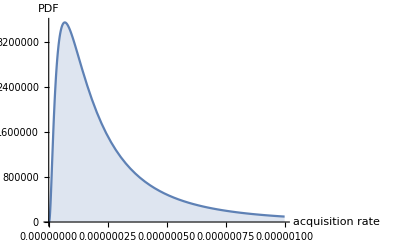

```mathematica
Plot[PDF[acquisitionDist,x],{x,0,10^-6},Filling->Axis,AxesLabel->{"acquisition rate","PDF"}]
```

```mathematica
acquisitionRates=RandomVariate[acquisitionDist, nSpacers];
```

```mathematica
numericalExampleRules=Join[
{nspacers->nSpacers,f0->1.0,m->50,μ->10,λ->1*^-3, ρ->1*^-3,p[0]->0.99},
Table[p[i]->deathRates[[i]],{i,1,nSpacers}],
Table[α[i]->acquisitionRates[[i]],{i,1,nSpacers}]];
```

```mathematica
stationaryPrediction=getStationaryState[numericalExampleRules]
```

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{x[0]→(rstar/(1+rstar)/.{}⟦1⟧),x[1]→(1),98,x[100]→1,v→(48.5+10 (0.00380974 (1/1/.{}⟦1⟧)+98+0.388604 1))/(20 (50 1+1) (1-10 (0.00380974 (1/1/.1)+98+1)))}
 |  |  |  |

```mathematica
capacityRule={nmax->1000};
```

```mathematica
numericalExampleConcEqns=getConcentrationEquations[nspacers/.numericalExampleRules]/.finiteGrowthRules[nspacers/.numericalExampleRules]/.reducedRules/.capacityRule;
```

```mathematica
numericalExampleConcICs={n[0][0]==1.0,v[0]==10}~Join~Table[n[i][0]==0,{i,1,nSpacers}];
```

```mathematica
tmax=32;
```

```mathematica
numericalSoln=NDSolve[Evaluate[Join[numericalExampleConcICs,(numericalExampleConcEqns/.numericalExampleRules)]],Evaluate[Join[Table[n[i],{i,0,(nspacers/.numericalExampleRules)}],{v}]],{t,0,tmax}];
```

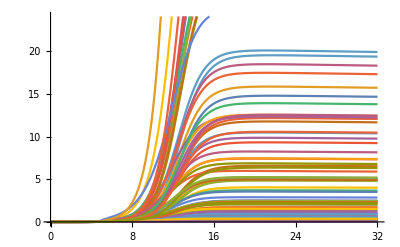

```mathematica
Plot[Evaluate[Table[n[i][t],{i,1,nSpacers}]/.numericalSoln],{t,0,tmax}]
```

```mathematica
finalRatios=Table[n[i][tmax]/.numericalSoln[[1]],{i,1,nSpacers}]/Sum[n[i][tmax]/.numericalSoln[[1]],{i,1,nSpacers}];
```

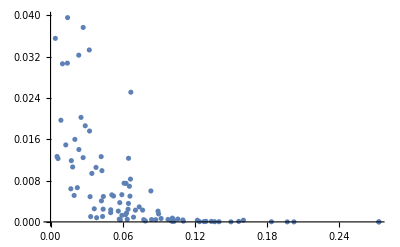

```mathematica
ListPlot[Transpose[{deathRates,finalRatios}]]
```

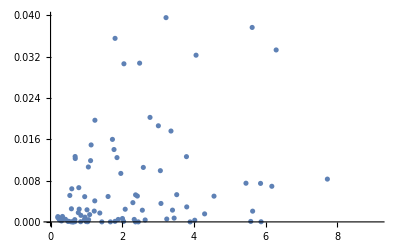

```mathematica
ListPlot[Transpose[{acquisitionRates,finalRatios}]]
```

# Scratch

## Two bacterial species

Set up equations

These are the basic equations. n is the fraction of bacteria without spacers; v is the concentration of viruses. k_1 is the rate at which spacers are lost, and v k_2 is the rate at which new spacers are acquired.

```mathematica
fullEqns={v'[t]==γ v[t]((m+1)n[t]-1), n'[t]==-Δf[v[t]] n[t](1-n[t])+k1 (1-n[t]) - k2 v[t] n[t]};
```

Rescale time to account for γ parameter (i.e., time will be measured in units of γ^-1). This also rescales the rates k_1, k_2, and Δf, since they contain time in their units. This makes k_1 and Δf dimensionless. k_2 now has the same dimensions as v^-1.

```mathematica
timeRescaleRules={t->t/γ,v->(v[γ #]&),n->(n[γ #]&),k1->γ k1, k2->γ k2, Δf->(γ Δf[#]&)};
assumptions={γ>0, k2>0};
```

```mathematica
eqns1=Assuming[assumptions,fullEqns/.timeRescaleRules//Simplify]
```

{(-1+(1+m) n[t]) v[t]==v'[t],n[t] (k1+k2 v[t]+Δf[v[t]])+n'[t]==k1+n[t]^2 Δf[v[t]]}

Rescale viral concentration to account for k_2. This makes v dimensionless (i.e., the viral concentration is measured in units of γ/k_2, where these are the parameters from the original equations).

```mathematica
vRescaleRule={v->(v[#]/k2&), Δf->(Δf[k2 #]&)};
```

```mathematica
rescaledEqns=Assuming[assumptions, eqns1/.vRescaleRule//Simplify]
```

{(-1+(1+m) n[t]) v[t]==v'[t],n[t] (k1+v[t]+Δf[v[t]])+n'[t]==k1+n[t]^2 Δf[v[t]]}

Find stationary states

## Trivial solution with vanishing viral population

One of the stationary states can be easily guessed: it occurs when there are no viruses at all, in which case the wildtype population takes over assuming k_1≠0 (because there is no cost associated to losing spacers). When k_1==0,  any value of n provides a solution when v==0.

```mathematica
rescaledEqns/.v->(0&)/.n->(1&)//Simplify
```

{True,True}

However, this solution is unstable.

```mathematica
tmp=Series[(rescaledEqns/.v->(ϵ δv[#]&)/.n->((1 - ϵ δn[#])&)//Simplify),{ϵ,0,1}]//Normal//Simplify;
linearizedEqnsTrivialSoln=Assuming[ϵ>0,tmp//Simplify]
```

{m δv[t]==δv'[t],(k1-Δf[0]) δn[t]+δn'[t]==δv[t]}

Plug in exponential solutions and get the matrix of the resulting system of equations for the amplitudes.

```mathematica
tmp=CoefficientArrays[Assuming[t∈Reals&&λ∈Reals,linearizedEqnsTrivialSoln/.δv->(δv0 Exp[λ #]&)/.δn->(δn0 Exp[λ #]&)//Simplify],{δv0, δn0}][[2]]//Normal;
MatrixForm[tmp]
```

(m-λ | 0
-1 | k1+λ-Δf[0])

Non-trivial solutions only exist if the determinant of this matrix is zero.

```mathematica
Solve[(Det[tmp]//Simplify)==0,λ]
```

{{λ→m},{λ→-k1+Δf[0]}}

Since there is always a linearized solution with λ>0, we conclude that the solution in which the viral population is zero is unstable.

## Other solutions -- Δf proportional to viral concentration

To find other solutions, we need to have an explicit form for Δf[v]. A natural assumption is to take Δf[v] = α v. This is the same reason for which the spacer acquisition is proportional to concentration: we assume that lysis, like spacer acquisition, is a stochastic event that occurs with a given fixed probability given an encounter with the virus. The probability of this encounter, in turn, is proportional to the viral concentration.

```mathematica
stationarityEqns=(rescaledEqns/.v->(vs&)/.n->(ns&)/.Δf->(α #&)//Simplify)
```

{(1+m) ns vs==vs,ns (k1+vs+vs α)==k1+ns^2 vs α}

One of the solutions is the one mentioned above. The other is:

```mathematica
nontrivialSolution=Solve[stationarityEqns, {ns, vs}][[2]]//Simplify
```

{ns→1/(1+m),vs→(k1 m (1+m))/(1+m+m α)}

## Other solutions -- constant Δf

We can also check what happens when the difference in fitness between the two bacterial strains is independent of the viral concentration Δf[v]. While it’s not immediately clear how to map this to CRISPR dynamics, it could be a useful approximation in cases in which the viral dynamics is slow.

```mathematica
stationarityEqnsConstFitness=(rescaledEqns/.v->(vs&)/.n->(ns&)/.Δf->(Δf&)//Simplify)
```

{(1+m) ns vs==vs,ns (k1+vs+Δf)==k1+ns^2 Δf}

Again we get one solution in which the virus disappears and the population is taken over by the wildtype bacteria, but now we have two other solutions.

```mathematica
nontrivialSolutionsConstFitness=Solve[stationarityEqnsConstFitness,{ns,vs}][[{2,3}]]//Simplify
```

{{ns→1/(1+m),vs→(m (k1+k1 m-Δf))/(1+m)},{ns→k1/Δf,vs→0}}

We should check the stability of these solutions.

### Solution with vanishing viral population

```mathematica
tmp=Series[Assuming[ϵ>0,rescaledEqns/.Δf->(Δf&)/.v->(vs + ϵ δv[#]&)/.n->(ns+ϵ δn[#]&)/.nontrivialSolutionsConstFitness[[2]]],{ϵ,0,1}]//Normal//Simplify;
linearizedEqnsConstFitnessNoVirus=Assuming[ϵ>0&&Δf≠0,Simplify[tmp]]
```

{(k1+k1 m-Δf) δv[t]==Δf δv'[t],Δf (-k1+Δf) δn[t]+k1 δv[t]+Δf δn'[t]==0}

Plug in exponential solutions and get the matrix of the resulting system of equations for the amplitudes.

```mathematica
tmp=CoefficientArrays[Assuming[t∈Reals&&λ∈Reals,linearizedEqnsConstFitnessNoVirus/.δv->(δv0 Exp[λ #]&)/.δn->(δn0 Exp[λ #]&)//Simplify],{δv0, δn0}][[2]]//Normal;
MatrixForm[tmp]
```

(k1 (1+m)-Δf (1+λ) | 0
-k1 | k1 Δf-Δf (Δf+λ))

```mathematica
Solve[(Det[tmp]//Simplify)==0,λ]
```

{{λ→k1-Δf},{λ→(k1+k1 m-Δf)/Δf}}

This solution is stable provided k_1<Δf/(m+1). (We’re assuming that Δf>0.)

```mathematica
Assuming[k1<Δf/(m+1)&&Δf>0&&m>0,λ<0/.Solve[(Det[tmp]//Simplify)==0,λ]//Simplify]
```

{True,True}

### Solution with non-vanishing viral population

Note that this needs k_1≥Δf/(m+1) in order to have v_s≥0.

```mathematica
tmp=Series[Assuming[ϵ>0,rescaledEqns/.Δf->(Δf&)/.v->(vs + ϵ δv[#]&)/.n->(ns+ϵ δn[#]&)/.nontrivialSolutionsConstFitness[[1]]],{ϵ,0,1}]//Normal//Simplify;
linearizedEqnsConstFitnessWithVirus=Assuming[ϵ>0&&Δf≠0,Simplify[tmp]]
```

{m (k1+k1 m-Δf) δn[t]==δv'[t],((k1 (1+m)^2-Δf) δn[t]+δv[t]+(1+m) δn'[t])/(1+m)==0}

Plug in exponential solutions and get the matrix of the resulting system of equations for the amplitudes.

```mathematica
tmp=CoefficientArrays[Assuming[t∈Reals&&λ∈Reals,linearizedEqnsConstFitnessWithVirus/.δv->(δv0 Exp[λ #]&)/.δn->(δn0 Exp[λ #]&)//Simplify],{δv0, δn0}][[2]]//Normal;
MatrixForm[tmp]
```

(-λ | k1 m (1+m)-m Δf
1/(1+m) | k1 (1+m)-Δf/(1+m)+λ/(1+m)+(m λ)/(1+m))

```mathematica
Solve[(Det[tmp]//Simplify)==0,λ]
```

{{λ→(-k1-2 k1 m-k1 m^2+Δf-√((k1+2 k1 m+k1 m^2-Δf)^2-4 (1+m) (k1 m+k1 m^2-m Δf)))/(2 (1+m))},{λ→(-k1-2 k1 m-k1 m^2+Δf+√((k1+2 k1 m+k1 m^2-Δf)^2-4 (1+m) (k1 m+k1 m^2-m Δf)))/(2 (1+m))}}

```mathematica
Assuming[Δf>0&&m>0&&k1>0,λ<0/.Solve[(Det[tmp]//Simplify)==0,λ]//Simplify]
```

{k1 (1+m)^2+√(k1^2 (1+m)^4-2 k1 (1+m)^2 (2 m+Δf)+Δf (4 m+4 m^2+Δf))>Δf,Δf+√(-4 m (1+m) (k1+k1 m-Δf)+(-k1 (1+m)^2+Δf)^2)<k1 (1+m)^2}

Dot dot dot...

## What happens when k_1==0? -- assuming Δf=α v

```mathematica
noSpacerLossEqns=rescaledEqns/.k1->0//Simplify
```

{(-1+(1+m) n[t]) v[t]==v'[t],n[t]^2 Δf[v[t]]==n[t] (v[t]+Δf[v[t]])+n'[t]}

```mathematica
noSpacerStationarityEqns=noSpacerLossEqns/.v->(vs&)/.n->(ns&)/.Δf->(α #&)//Simplify
```

{(1+m) ns vs==vs,ns^2 vs α==ns vs (1+α)}

When the viral population vanishes, we have a flat direction (every constant value of n gives a stationary solution). The actual asymptotic solution will depend on the initial conditions.

```mathematica
noSpacerStationarityEqns/.vs->0
```

{True,True}

### Numerical solutions

```mathematica
numericalRules={m->3,α->0.05};
initialConditions={v[0]==0.005,n[0]==0.5};
tmax=40;
```

```mathematica
soln=NDSolve[Join[noSpacerLossEqns/.Δf->(α #&)/.numericalRules, initialConditions],{n,v},{t,0,tmax}][[1]]
```

{n→InterpolatingFunction[{{0., 40.}}, <>],v→InterpolatingFunction[{{0., 40.}}, <>]}

```mathematica
{n[tmax],v[tmax]}/.soln
```

{0.100045,1.09684×10^-9}

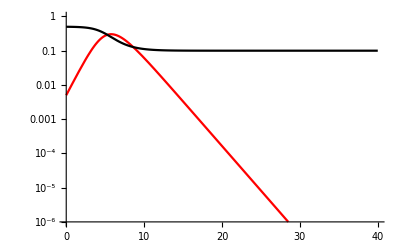

```mathematica
LogPlot[Evaluate[{v[t],n[t]}/.soln],{t,0,tmax},PlotRange->{10^-6,1},PlotStyle->{Red,Black}]
```

#### Can we add noise in a simple manner?

I’m interested in a simple solution that does not involve solving an SDE. The basic idea is that adding noise at infinitely fine timescales is anyway not realistic, so we can use the usual NDSolve, but add randomly-generated functions. This may end up being slower than solving the SDE, though, so I should consider doing that.

The following function generates a function defined on the given range that takes i.i.d. Gaussian values with mean 0 and standard deviation 1 and that varies or timescales given by dt. This works by generating equally-spaced discrete samples, and then interpolating through them.

```mathematica
tmax=400;
```

```mathematica
generateRandomFunction[range_,dt_]:=Interpolation[Table[{t,RandomVariate[NormalDistribution[0,1]]},{t,range[[1]],range[[2]],dt}]];
```

```mathematica
noiseEqns=noSpacerLossEqns/.x_'[t]:>x'[t]+0.01x[t]generateRandomFunction[{0,tmax},0.1][t]
```

{(-1+(1+m) n[t]) v[t]==0.01 v[t] InterpolatingFunction[{{0., 400.}}, <>][t]+v'[t],n[t]^2 Δf[v[t]]==n[t] (v[t]+Δf[v[t]])+0.01 n[t] InterpolatingFunction[{{0., 400.}}, <>][t]+n'[t]}

```mathematica
noiseSoln=NDSolve[Join[noiseEqns/.Δf->(α #&)/.numericalRules, initialConditions],{n,v},{t,0,tmax}][[1]]
```

{n→InterpolatingFunction[{{0., 400.}}, <>],v→InterpolatingFunction[{{0., 400.}}, <>]}

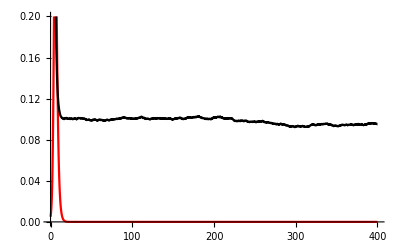

```mathematica
Plot[Evaluate[{v[t],n[t]}/.noiseSoln],{t,0,tmax},PlotRange->{0,0.2},PlotStyle->{Red,Black}]
```

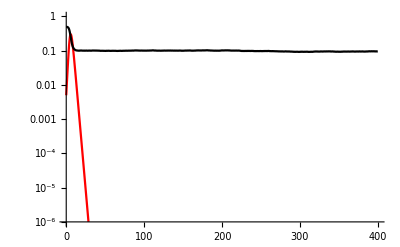

```mathematica
LogPlot[Evaluate[{v[t],n[t]}/.noiseSoln],{t,0,tmax},PlotRange->{10^-6,1},PlotStyle->{Red,Black}]
```

## What happens when k_1==0? -- assuming Δf=const.

```mathematica
noSpacerLossEqnsConstFitness=rescaledEqns/.k1->0/.Δf->(Δf&)//Simplify
```

{(-1+(1+m) n[t]) v[t]==v'[t],Δf n[t]^2==n[t] (Δf+v[t])+n'[t]}

```mathematica
noSpacerConstFitnessStationarityEqns=noSpacerLossEqnsConstFitness/.v->(vs&)/.n->(ns&)//Simplify
```

{(1+m) ns vs==vs,ns^2 Δf==ns (vs+Δf)}

```mathematica
Solve[noSpacerConstFitnessStationarityEqns,{ns,vs}]
```

{{ns→-1/(-1-m),vs→-(m Δf)/(1+m)},{ns→0,vs→0},{ns→1,vs→0}}

Note that the first option is not actually a solution in the case Δf>0 which we’ve been focusing on, since it leads to a negative viral population.

Should check the stability of the other two solutions.

Some numerical solutions

```mathematica
numericalRules={m->3,k1->0.04,α->0.05};
tmax=90;
```

Set initial conditions.

```mathematica
initialConds={v[0]==0.01,n[0]==0.99};
```

```mathematica
numericalEqns=rescaledEqns/.Δf->(α #&)/.numericalRules
```

{(-1+4 n[t]) v[t]==v'[t],n[t] (0.04+1.05 v[t])+n'[t]==0.04+0.05 n[t]^2 v[t]}

```mathematica
soln=NDSolve[Join[numericalEqns,initialConds],{n,v},{t,0.0,tmax}]
```

{{n→InterpolatingFunction[{{0., 90.}}, <>],v→InterpolatingFunction[{{0., 90.}}, <>]}}

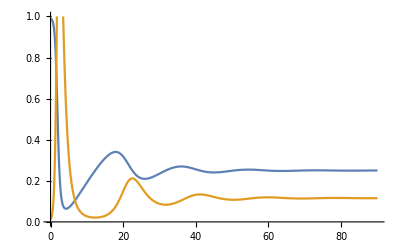

```mathematica
Plot[Evaluate[{n[t],v[t]}/.soln],{t,0,tmax},PlotRange->{0,1}]
```

## Several bacterial species -- Δf=α v

Three bacterial species

```mathematica
threeBacteriaEqns={
n0'[t]==-(α1 n1[t]+α2 n2[t])v[t]n0[t]+k(1-n0[t])-v[t] n0[t],
n1'[t]==(α1-α1 n1[t] - α2 n2[t])v[t] n1[t]-k n1[t]+1/2 v[t] n0[t],
n2'[t]==(α2-α1 n1[t] - α2 n2[t])v[t] n2[t]-k n2[t]+1/2 v[t] n0[t],
v'[t]==v[t]((m+1)n0[t]-1)
};
```

## Numerical solutions

```mathematica
numericalRules={m->3,k->0.04,α1->0.05, α2->0.02};
tmax=90;
```

Set initial conditions.

```mathematica
initialConds={v[0]==0.005,n0[0]==0.9, n1[0]==0.07,n2[0]==0.03};
```

```mathematica
numericalEqns=threeBacteriaEqns/.numericalRules
```

{n0'[t]==0.04 (1-n0[t])-n0[t] v[t]+n0[t] (-0.05 n1[t]-0.02 n2[t]) v[t],n1'[t]==-0.04 n1[t]+1/2 n0[t] v[t]+n1[t] (0.05-0.05 n1[t]-0.02 n2[t]) v[t],n2'[t]==-0.04 n2[t]+1/2 n0[t] v[t]+(0.02-0.05 n1[t]-0.02 n2[t]) n2[t] v[t],v'[t]==(-1+4 n0[t]) v[t]}

```mathematica
soln=NDSolve[Join[numericalEqns,initialConds],{n0,n1,n2,v},{t,0.0,tmax}]
```

{{n0→InterpolatingFunction[{{0., 90.}}, <>],n1→InterpolatingFunction[{{0., 90.}}, <>],n2→InterpolatingFunction[{{0., 90.}}, <>],v→InterpolatingFunction[{{0., 90.}}, <>]}}

Find λ.

```mathematica
λRule=NSolve[(1/(λ-m α1)+1/(λ-m α2)/.numericalRules)==2&&(λ>m Max[α1,α2]/.numericalRules),λ][[1]]
```

{λ→1.10702}

Find the stationary solutions.

```mathematica
stationarityRules0={n0star->1/(m+1),n1star->1/2 m/(m+1)1/(λ-m α1),n2star->1/2 m/(m+1)1/(λ-m α2)}/.numericalRules/.λRule;
stationarityRules = Join[stationarityRules0,{vstar->(m k)/(1 + n1star α1 + n2star α2)}/.numericalRules/.stationarityRules0]
```

{n0star→1/4,n1star→0.391841,n2star→0.358159,vstar→0.116873}

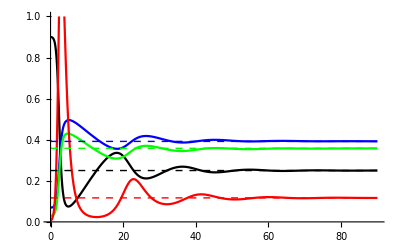

```mathematica
Plot[Evaluate[Join[{n0[t],n1[t],n2[t],v[t]}/.soln,{n0star,n1star,n2star,vstar}/.stationarityRules]],{t,0,tmax},PlotRange->{0,1.0},PlotStyle->{Black, Blue,Green, Red,{Dashed,Thin,Black}, {Dashed,Thin,Blue}, {Dashed,Thin,Green}, {Dashed,Thin,Red}}]
```

## Scratch

Two bacterial species

These are the basic equations. n is the fraction of bacteria without spacers; v is proportional to the number of viruses.

```mathematica
eqns={D[v[t],t]==v[t](m1 n[t]-1),D[n[t],t]==Δf v[t] n[t]^2 - (Δf+1)n[t]v[t]};
```

## Attempts to solve the equations exactly

```mathematica
solns=DSolve[eqns,{v[t],n[t]},t]
```

{{v[t]→C[1]+1/(Δf (1+Δf))(Δf Log[InverseFunction[∫_1^#1 (1/(K[1] (-1-Δf+Δf K[1]) (Δf C[1]+Δf^2 C[1]+Δf Log[K[1]]+m1 Log[1+Δf-Δf K[1]]-Δf Log[1+Δf-Δf K[1]]+m1 Δf Log[1+Δf-Δf K[1]])))ⅆK[1]&][t/(Δf (1+Δf))+C[2]]]+(m1-Δf+m1 Δf) Log[1+Δf-Δf InverseFunction[∫_1^#1 (1/(K[1] (-1-Δf+Δf K[1]) (Δf C[1]+Δf^2 C[1]+Δf Log[K[1]]+m1 Log[1+Δf-Δf K[1]]-Δf Log[1+Δf-Δf K[1]]+m1 Δf Log[1+Δf-Δf K[1]])))ⅆK[1]&][t/(Δf (1+Δf))+C[2]]]),n[t]→InverseFunction[∫_1^#1 (1/(K[1] (-1-Δf+Δf K[1]) (Δf C[1]+Δf^2 C[1]+Δf Log[K[1]]+m1 Log[1+Δf-Δf K[1]]-Δf Log[1+Δf-Δf K[1]]+m1 Δf Log[1+Δf-Δf K[1]])))ⅆK[1]&][t/(Δf (1+Δf))+C[2]]}}

```mathematica
ansatz={v[t]->v0 t^α Exp[-β t],n[t]->(t+α-β t)/(m1 t)};
```

```mathematica
deransatz=ansatz/.(A_[t]->B_):>(A'[t]->D[B, t])//Simplify
```

{v'[t]→ⅇ^(-t β) t^(-1+α) v0 (α-t β),n'[t]→-α/(m1 t^2)}

```mathematica
allansatz=Join[ansatz,deransatz]
```

{v[t]→ⅇ^(-t β) t^α v0,n[t]→(t+α-t β)/(m1 t),v'[t]→ⅇ^(-t β) t^(-1+α) v0 (α-t β),n'[t]→-α/(m1 t^2)}

```mathematica
rules={α->0,β->(-m1+Δf-m1 Δf)/Δf};
```

```mathematica
tmp=eqns/.allansatz/.rules//Simplify
```

{True,True}

```mathematica
n[t]/.ansatz/.rules//Simplify
```

1+1/Δf

```mathematica
Collect[-(t+α-t β) Δf+m1 t (1+Δf), t]
```

-α Δf+t (-Δf+β Δf+m1 (1+Δf))

```mathematica
Solve[-Δf+β Δf+m1 (1+Δf)==0,β]
```

{{β→(-m1+Δf-m1 Δf)/Δf}}

```mathematica
Solve[tmp[[1]],n[t]][[1]]
```

{n[t]→(t+α-t β)/(m1 t)}

```mathematica
eqns[[2]]
```

n'[t]==-(1+Δf) n[t] v[t]+Δf n[t]^2 v[t]

```mathematica
neweq2=(Solve[eqns[[2]]/.n->(n[#]/(Δf v[#])&)//Simplify,n'[t]][[1]]//Simplify//Expand)/.(A_->B_)->(A==B)
```

{n'[t]==n[t]^2-n[t] v[t]-Δf n[t] v[t]+(n[t] v'[t])/v[t]}

```mathematica
newereq2=(Solve[neweq2/.n->(-D[u[#], #]/u[#]&)//Simplify,u''[t]][[1]]//Simplify)/.(A_->B_)->(A==B)
```

{u''[t]==-(u'[t] ((1+Δf) v[t]^2-v'[t]))/v[t]}

```mathematica
(eqns[[1]]/.n->(n[#]/(Δf v[#])&)//Simplify)/.n->(-D[u[#], #]/u[#]&)
```

-(m1 u'[t])/(Δf u[t])==v[t]+v'[t]

```mathematica
newsystem={(eqns[[1]]/.n->(n[#]/(Δf v[#])&)//Simplify)/.n->(-D[u[#], #]/u[#]&),newereq2[[1]]}
```

{-(m1 u'[t])/(Δf u[t])==v[t]+v'[t],u''[t]==-(u'[t] ((1+Δf) v[t]^2-v'[t]))/v[t]}

## Approximations

### Low viral and no-spacer bacteria concentrations

We will assume that the viral concentration is small enough that the initial change in the numbers of bacteria is slow enough to be ignored for the viral dynamics. For this to happen, the fraction of bacteria that don’t have spacers needs to be  below 1/m1, otherwise the viral numbers would quickly increase.

```mathematica
eqnsLowVirus={eqns[[1]]/.n->(n0&), eqns[[2]]}
```

{v'[t]==(-1+m1 n0) v[t],n'[t]==-(1+Δf) n[t] v[t]+Δf n[t]^2 v[t]}

Now we can solve for the viral dynamics.

```mathematica
viralSoln0LowVirus=DSolve[eqnsLowVirus[[1]],v,t][[1]]
```

{v→Function[{t},ⅇ^((-1+m1 n0) t) C[1]]}

Set the initial condition.

```mathematica
viralSolnLowVirus=Evaluate[viralSoln0LowVirus/.Solve[(v[0]/.viralSoln0LowVirus)==v0,C[1],Reals][[1]]]
```

{v→Function[{t},ⅇ^((-1+m1 n0) t) v0]}

And plug it into the equation for the bacterial population

```mathematica
bacterialEqnLowVirus=eqnsLowVirus[[2]]/.viralSolnLowVirus//Simplify
```

n'[t]==ⅇ^((-1+m1 n0) t) v0 n[t] (-1-Δf+Δf n[t])

Now this one should be solvable, right?

```mathematica
bacterialSoln0LowVirus=DSolve[bacterialEqnLowVirus, n,t][[1]]//Simplify
```

{n→Function[{t},(1+Δf)/(ⅇ^((ⅇ^((-1+m1 n0) t) v0)/(-1+m1 n0)+C[1]+Δf ((ⅇ^((-1+m1 n0) t) v0)/(-1+m1 n0)+C[1]))+Δf)]}

Let’s impose initial conditions.

```mathematica
initialCondLowVirus=Assuming[Δf>0&&m1>1&&n0<1/m1&&n0>0,Solve[(n[0]/.bacterialSoln0LowVirus//Simplify)==n0,C[1], Reals][[1]]//Simplify]
```

{C[1]→(-v0 (1+Δf)+(-1+m1 n0) Log[(1+Δf-n0 Δf)/n0])/((-1+m1 n0) (1+Δf))}

```mathematica
bacterialSolnLowVirus=Evaluate[bacterialSoln0LowVirus/.initialCondLowVirus//Simplify]
```

{n→Function[{t},(1+Δf)/(ⅇ^((ⅇ^((-1+m1 n0) t) v0)/(-1+m1 n0)+(-v0 (1+Δf)+(-1+m1 n0) Log[(1+Δf-n0 Δf)/n0])/((-1+m1 n0) (1+Δf))+Δf ((ⅇ^((-1+m1 n0) t) v0)/(-1+m1 n0)+(-v0 (1+Δf)+(-1+m1 n0) Log[(1+Δf-n0 Δf)/n0])/((-1+m1 n0) (1+Δf))))+Δf)]}

That looks ugly... What’s the asymptotic bacterial population?

```mathematica
asymptoticNLowVirus=Assuming[Δf>0&&m1>1&&n0<1/m1&&n0>0&&v0>0,Limit[n[t]/.bacterialSolnLowVirus, t->Infinity]]
```

(ⅇ^((v0 (1+Δf))/(-1+m1 n0)) n0 (1+Δf))/(1+(1+(-1+ⅇ^((v0 (1+Δf))/(-1+m1 n0))) n0) Δf)

We started with the assumption that v0 was small, so let’s see what that approximation gives us.

```mathematica
asymptoticNApproxLowVirus=Normal[Series[asymptoticNLowVirus,{v0,0,1}]]
```

n0-(n0 v0 (-1-Δf+n0 Δf))/(-1+m1 n0)

Let’s test this!

```mathematica
testRules={m1->4,Δf->0.1};
testIniRules={v0->0.01,n0->0.2};
```

```mathematica
testNAsymptotic=asymptoticNLowVirus/.testRules/.testIniRules
```

0.189481

```mathematica
testSolution=NDSolve[Join[Evaluate[eqns/.testRules],Evaluate[{n[0]==n0,v[0]==v0}/.testIniRules]],{n,v},{t,0, 20}];
```

```mathematica
n[20]/.testSolution
```

{0.190475}

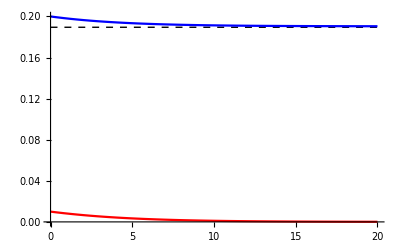

```mathematica
Plot[Evaluate[Prepend[{n[t],v[t]}/.testSolution,testNAsymptotic]],{t,0,20},PlotStyle->{{Black,Dashed,Thin},Blue,Red}]
```

## Analytical solutions for stationary states

```mathematica
vRule={v->μ/(1 + favg-(1-p)n0)(1-n0)/n0};
n0Rule={n0->(1-favg)/(m+1)};
niRule={ni->(αi v n0)/(μ-(favg-fi)v - v n0 (1-p))};
```

```mathematica
vRule/.n0Rule//Simplify
```

{v→-((1+m) (favg+m) μ)/((-1+favg) (m+favg (2+m-p)+p))}

```mathematica
niRule/.vRule/.n0Rule//Simplify
```

{ni→((-1+favg) (favg+m) αi)/((1+m) (2 favg^2-fi m-p+favg (-1-fi+m+p)))}

```mathematica
Solve[2 favg^2-fi m-p+favg (-1-fi+m+p)==0,fi]//Simplify
```

{{fi→(2 favg^2-p+favg (-1+m+p))/(favg+m)}}

## Analytical solutions for stationary states -- #2

```mathematica
wtEq={(f0-favg)x0 - ρ(p0-pavg)v x0-ρ v x0 αtot + λ(1-x0)==0};
spacerEq={(fi-favg)xi-ρ(pi-pavg) v xi +ρ v x0 αi -λ xi==0};
virusEq={ρ v n (x0 p0 (m0+1) + pmavg +pavg-1)==0};
```

```mathematica
soln=Solve[Join[wtEq,spacerEq,virusEq],{x0,xi,v}]//Simplify
```

{{x0→λ/(-f0+favg+λ),xi→0,v→0},{x0→-(-1+pavg+pmavg)/((1+m0) p0),xi→((-1+pavg+pmavg) αi (-f0 (-1+pavg+pmavg)+favg (-1+pavg+pmavg)+(-1+p0+m0 p0+pavg+pmavg) λ))/((1+m0) p0 (f0 pavg-f0 pavg^2-f0 pi+f0 pavg pi-f0 pavg pmavg+f0 pi pmavg-fi (-1+pavg+pmavg) (p0-pavg+αtot)+favg (-1+pavg+pmavg) (p0-pi+αtot)-p0 λ+2 p0 pavg λ+m0 p0 pavg λ+pi λ-p0 pi λ-m0 p0 pi λ-pavg pi λ+p0 pmavg λ-pi pmavg λ-αtot λ+pavg αtot λ+pmavg αtot λ)),v→(-f0 (-1+pavg+pmavg)+favg (-1+pavg+pmavg)+(-1+p0+m0 p0+pavg+pmavg) λ)/((-1+pavg+pmavg) (-p0+pavg-αtot) ρ)}}

```mathematica
Series[(v/.soln[[2]]/.pmavg->m0 pavg/.pavg->ϵ pavg//Simplify),{ϵ,0,1}]//Simplify
```

(f0-favg+(-1+p0+m0 p0) λ)/((p0+αtot) ρ)+(pavg (f0-favg+(-1+(1+m0)^2 p0^2+(1+m0) p0 (1+αtot+m0 αtot)) λ) ϵ)/((p0+αtot)^2 ρ)+O[ϵ]^2

```mathematica
Series[(xi/.soln[[2]]/.pmavg->m0 pavg/.pavg->ϵ pavg/.pi->ϵ pi//Simplify),{ϵ,0,1}]//Simplify
```

(αi (f0-favg+(-1+p0+m0 p0) λ))/((1+m0) p0 (p0+αtot) (favg-fi+λ))+(αi (f0^2 (pavg-pi)+favg^2 ((1+m0) p0 pavg-pi+(1+m0) pavg αtot)+λ (-fi pavg (-1+2 (1+m0) p0+αtot+m0 αtot)+((1+m0)^2 p0^2 (pavg-pi)-pi+2 (1+m0) p0 pi+(1+m0) pavg αtot) λ)-f0 (-fi pavg (-1+p0+m0 p0+αtot+m0 αtot)+favg (-2 pi+pavg (1+p0+m0 p0+αtot+m0 αtot))+(2 (-1+p0+m0 p0) pi+pavg (1-(1+m0) p0+αtot+m0 αtot)) λ)+favg (-fi pavg (-1+p0+m0 p0+αtot+m0 αtot)+((1+m0) p0 (pavg+2 pi)+2 (-pi+(1+m0) pavg αtot)) λ)) ϵ)/((1+m0) p0 (p0+αtot)^2 (favg-fi+λ)^2)+O[ϵ]^2

## Analytical solutions for stationary states -- #3

```mathematica
eqns={
-ρ(p0(1-x0)-pbar)v x0-v x0 αtot+λ(1-x0)==0,
-ρ(pi-pbar-p0 x0)v xi +αi v x0-λ xi==0,
ρ v n(x0 p0 mhat+μhat pbar-1)==0
};
```

```mathematica
solns=Solve[eqns,{v,x0,xi}]//Simplify
```

{{v→0,x0→1,xi→0},{v→-(mhat λ (-1+mhat p0+pbar μhat))/((-1+pbar μhat) ((-1+pbar μhat) ρ+mhat (αtot+(p0-pbar) ρ))),x0→(1-pbar μhat)/(mhat p0),xi→(αi (-1+pbar μhat) (-1+mhat p0+pbar μhat))/(mhat p0 (αtot (-1+pbar μhat)+(mhat p0 (pbar-pi)+pi-pbar pi μhat) ρ))}}

```mathematica
Series[v/.solns[[2]],{pbar,0,1}]//Simplify//Normal
```

(mhat (-1+mhat p0) λ)/(-ρ+mhat (αtot+p0 ρ))+(mhat pbar λ (μhat ρ+mhat^2 p0 (αtot μhat+ρ+p0 μhat ρ)-mhat (ρ+2 p0 μhat ρ)))/(ρ-mhat (αtot+p0 ρ))^2

```mathematica
(Series[xi/.solns[[2]]/.pbar->ϵ pbar/.pi->ϵ pi//Simplify,{ϵ,0,1}]//Simplify//Normal)/.ϵ->1//Simplify
```

(αi (αtot (-1+mhat p0+pbar μhat)+(-1+mhat p0) (mhat p0 (pbar-pi)+pi) ρ))/(mhat p0 αtot^2)

```mathematica
αi/(mhat p0)((1-μhat pbar)(mhat p0 + μhat pbar - 1))/((αtot - ρ pi)(1-μhat pbar) + ρ mhat p0(pi - pbar))-(xi/.solns[[2]])//Simplify
```

0

```mathematica
(mhat λ)/(1-μhat pbar)(mhat p0 + μhat pbar - 1)/(mhat(αtot+ρ(p0-pbar))-ρ(1-μhat pbar))-(v/.solns[[2]])//Simplify
```

0

```mathematica
rRule={r->(1-μhat pbar)/(mhat p0 + μhat pbar - 1)};
```

```mathematica
1/ρ r/(1+r)αi/(pi + r(αtot/ρ+(mhat p0-1)/μhat)-1/μhat)- xi/.solns[[2]]/.rRule//Simplify
```

0

```mathematica
1/ρ x0 αi/(pi + x0/(1-x0)(αtot/ρ+(mhat p0-1)/μhat)-1/μhat)- xi/.solns[[2]]//Simplify
```

0